# The Mobile 3rd Space

## Declare Base Constants

## Declare Thermal Resistances

## Equations

```mathematica
eqn={Ttile'[t]==(Q-(Ttile[t]-Tair[t])/Rair)/Ctile,(Ttile[t]-Tair[t])/Rair==(Tair[t]-Tout)/U+(Tair[t]-Tout)/Rwindow,Tair[0]==21}
```

{Ttile'[t]==(Q-(-Tair[t]+Ttile[t])/Rair)/Ctile,(-Tair[t]+Ttile[t])/Rair==(-Tout+Tair[t])/Rwindow+(-Tout+Tair[t])/U,Tair[0]==21}

```mathematica
sol=DSolveValue[eqn,{Ttile[t],Tair[t]},t];
airTemp=sol⟦2⟧
```

1/(Rwindow+U)ⅇ^(-(t (Rwindow+U))/(Ctile (Rair Rwindow+Rair U+Rwindow U))) (21 Rwindow-Rwindow Tout+ⅇ^((t (Rwindow+U))/(Ctile (Rair Rwindow+Rair U+Rwindow U))) Rwindow Tout+21 U-Q Rwindow U+ⅇ^((t (Rwindow+U))/(Ctile (Rair Rwindow+Rair U+Rwindow U))) Q Rwindow U-Tout U+ⅇ^((t (Rwindow+U))/(Ctile (Rair Rwindow+Rair U+Rwindow U))) Tout U)

```mathematica
eqn2={C1 Ttile'[t]==Q-(Ttile[t]-Twall[t])/Reff,C2 Twall'[t]==(Ttile[t]-Twall[t])/Reff-(Twall[t]-Tout)/R4,Ttile[0]==100,Twall[0]==50} (* + 3 is from -Tout @ Tout=-3*)
```

{C1 Ttile'[t]==Q-(Ttile[t]-Twall[t])/Reff,C2 Twall'[t]==(Ttile[t]-Twall[t])/Reff-(-Tout+Twall[t])/R4,Ttile[0]==100,Twall[0]==50}

```mathematica
sol=DSolveValue[eqn2,{Ttile[t],Twall[t]},t]
```

{-(2 ⅇ^-1 Reff^2 (100 C1^3 C2 ⅇ^(((1) t)/(C1 C2 R4 Reff^2)) R4^3 Reff+150+C1^2 C2 ⅇ^1 R4 Reff √(-4 C1 C2 R4 Reff^3+(1)^2) Tout))/((C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2+2 C1^2 R4 Reff-2 C1 C2 R4 Reff+C1^2 Reff^2) (5+√1) (C1 R4 Reff+C2 R4 Reff+C1 Reff^2+√(-4 C1 C2 R4 Reff^3+(1)^2))),-1/1}
 |  |  |  |

```mathematica
tileTemp=sol⟦1⟧;
wallTemp=sol⟦2⟧;
airTemp=wallTemp+((tileTemp-wallTemp)(Reff-R1))/Reff
```

-(2 ⅇ^(-1/1) Reff^2 (50 C1^3 C2 ⅇ^(((1) t)/(C1 C2 R4 Reff^2)) R4^3 Reff+130))/((C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2+2 C1^2 R4 Reff-2 C1 C2 R4 Reff+C1^2 Reff^2) (5+√1) (C1 R4 Reff+C2 R4 Reff+C1 Reff^2+√(-4 C1 C2 R4 Reff^3+(1)^2)))+((-R1+Reff) (1-1))/Reff
 |  |  |  |

```mathematica
CopyToClipboard[airTemp];
```

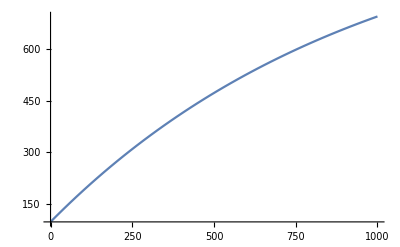

```mathematica
Plot[airTemp/.{R1->6,Reff->100,R4->6,C1->9,C2->9,C3->9,Q->10,Tout->21,C[1]->4},{t,0,1000}]
```

## Solve Take 2

## Solving